# 20 Gaussian Elimination: LU Decomposition

We know how to solve triangular systems of equations.  We are going to see how to reduce a general system 
	A.x=b 
to two triangular systems.

### Simple Matrices

What does the matrix below do?

```mathematica
L3=IdentityMatrix[8]; L3⟦4;;8,3⟧={L43,L53,L63,L73,L83};
MatrixForm[L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | L83 | 0 | 0 | 0 | 0 | 1)

Can you just write down its inverse?

```mathematica
MatrixForm[Inverse[L3]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | -L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | -L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | -L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | -L83 | 0 | 0 | 0 | 0 | 1)

### Multiplying Simple Matrices

Here is another “similar” matrix

```mathematica
L4=IdentityMatrix[8]; L4⟦5;;8,4⟧={L54,L64,L74,L84};
MatrixForm[L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | L54 | 1 | 0 | 0 | 0
0 | 0 | 0 | L64 | 0 | 1 | 0 | 0
0 | 0 | 0 | L74 | 0 | 0 | 1 | 0
0 | 0 | 0 | L84 | 0 | 0 | 0 | 1)

The product L3.L4 is simple

```mathematica
MatrixForm[L3.L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83 | L84 | 0 | 0 | 0 | 1)

However, the product L4.L3 is not. To use these matrices we need to wrok down.

```mathematica
MatrixForm[L4.L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53+L43 L54 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63+L43 L64 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73+L43 L74 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83+L43 L84 | L84 | 0 | 0 | 0 | 1)

### Chaining Simple Matrices

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

The lower triangular matrix below is the product of 7 of these simple matrices.

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
L21 | 1 | 0 | 0 | 0 | 0 | 0 | 0
L31 | L32 | 1 | 0 | 0 | 0 | 0 | 0
L41 | L42 | L43 | 1 | 0 | 0 | 0 | 0
L51 | L52 | L53 | L54 | 1 | 0 | 0 | 0
L61 | L62 | L63 | L64 | L65 | 1 | 0 | 0
L71 | L72 | L73 | L74 | L75 | L76 | 1 | 0
L81 | L82 | L83 | L84 | L85 | L86 | L87 | 1)

## Using these Simple Matrices to Create Zeros

### Manually

Gaussian Elimination is the first way people worked out to make zeros. Note, if you were solving equations by candle light in 18XX you would not organize it this way!

```mathematica
m=8;
A0=RandomReal[{-1,1},{m,m}];
L1=IdentityMatrix[m]; L1⟦2;;m,1⟧=A0⟦2;;m,1⟧/A0⟦1,1⟧;
MatrixForm[A1 = Chop[Inverse[L1].A0]]
```

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0.321566 | -0.183948 | -0.242045 | 0.48571 | -1.37477 | -0.323628 | -0.61579
0 | 0.693559 | 1.30083 | -0.639044 | 0.287107 | 0.459307 | 0.527598 | 0.301333
0 | 0.280713 | 1.14011 | 1.1244 | -0.101875 | 1.6819 | -0.630708 | -0.871342
0 | -0.343789 | 0.148495 | 0.81393 | -0.989712 | 0.959698 | -0.0172617 | -0.121803
0 | 0.561979 | 1.40292 | -0.29474 | 0.196204 | -0.386727 | 0.363406 | 0.0502908
0 | 0.313807 | -0.696718 | -0.188015 | -0.610225 | -0.53554 | -0.620467 | 0.837404)

If we do it again we can make another almost column of zeros.

```mathematica
L2=IdentityMatrix[m]; L2⟦3;;m,2⟧=A1⟦3;;m,2⟧/A1⟦2,2⟧;
MatrixForm[A2 = Chop[Inverse[L2].A1]]
```

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0 | 0.138171 | 0.536894 | 1.22012 | 0.537653 | 0.208687 | 0.132978
0 | 0 | 1.99558 | 1.04098 | 1.8711 | 4.58405 | 1.6757 | 1.91629
0 | 0 | 1.4213 | 1.80438 | 0.539237 | 3.35137 | -0.166019 | -0.2177
0 | 0 | -0.195885 | -0.018839 | -1.77488 | -1.08489 | -0.586364 | -0.922316
0 | 0 | 1.96587 | 1.06656 | 1.47969 | 2.95549 | 1.2937 | 1.35886
0 | 0 | -0.382371 | 0.572128 | 0.106468 | 1.33074 | -0.100997 | 1.5681)

We can keep going.

```mathematica
L3=IdentityMatrix[m]; L3⟦4;;m,3⟧=A2⟦4;;m,3⟧/A2⟦3,3⟧;
MatrixForm[A3 = Chop[Inverse[L3].A2]]
L4=IdentityMatrix[m]; L4⟦5;;m,4⟧=A3⟦5;;m,4⟧/A3⟦4,4⟧;
MatrixForm[A4 = Chop[Inverse[L4].A3]]
L5=IdentityMatrix[m]; L5⟦6;;m,5⟧=A4⟦6;;m,5⟧/A4⟦5,5⟧;
MatrixForm[A5 = Chop[Inverse[L5].A4]]
L6=IdentityMatrix[m]; L6⟦7;;m,6⟧=A5⟦7;;m,6⟧/A5⟦6,6⟧;
MatrixForm[A6 = Chop[Inverse[L6].A5]]
L7=IdentityMatrix[m]; L7⟦8;;m,7⟧=A6⟦8;;m,7⟧/A6⟦7,7⟧;
MatrixForm[A7 = Chop[Inverse[L7].A6]]
```

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0 | 0.138171 | 0.536894 | 1.22012 | 0.537653 | 0.208687 | 0.132978
0 | 0 | 0 | -6.71326 | -15.7509 | -3.18115 | -1.33832 | -0.00427908
0 | 0 | 0 | -3.71839 | -12.0116 | -2.17921 | -2.31269 | -1.58558
0 | 0 | 0 | 0.742315 | -0.0451106 | -0.322656 | -0.290508 | -0.733793
0 | 0 | 0 | -6.57222 | -15.8799 | -4.69409 | -1.67545 | -0.533108
0 | 0 | 0 | 2.05791 | 3.483 | 2.81862 | 0.476519 | 1.9361)

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0 | 0.138171 | 0.536894 | 1.22012 | 0.537653 | 0.208687 | 0.132978
0 | 0 | 0 | -6.71326 | -15.7509 | -3.18115 | -1.33832 | -0.00427908
0 | 0 | 0 | 0 | -3.28738 | -0.417213 | -1.57141 | -1.58321
0 | 0 | 0 | 0 | -1.78676 | -0.67441 | -0.438492 | -0.734266
0 | 0 | 0 | 0 | -0.459925 | -1.57978 | -0.365245 | -0.528919
0 | 0 | 0 | 0 | -1.34534 | 1.84346 | 0.0662638 | 1.93479)

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0 | 0.138171 | 0.536894 | 1.22012 | 0.537653 | 0.208687 | 0.132978
0 | 0 | 0 | -6.71326 | -15.7509 | -3.18115 | -1.33832 | -0.00427908
0 | 0 | 0 | 0 | -3.28738 | -0.417213 | -1.57141 | -1.58321
0 | 0 | 0 | 0 | 0 | -0.447646 | 0.415599 | 0.126239
0 | 0 | 0 | 0 | 0 | -1.5214 | -0.145395 | -0.307418
0 | 0 | 0 | 0 | 0 | 2.0142 | 0.709354 | 2.58271)

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0 | 0.138171 | 0.536894 | 1.22012 | 0.537653 | 0.208687 | 0.132978
0 | 0 | 0 | -6.71326 | -15.7509 | -3.18115 | -1.33832 | -0.00427908
0 | 0 | 0 | 0 | -3.28738 | -0.417213 | -1.57141 | -1.58321
0 | 0 | 0 | 0 | 0 | -0.447646 | 0.415599 | 0.126239
0 | 0 | 0 | 0 | 0 | 0 | -1.55788 | -0.736463
0 | 0 | 0 | 0 | 0 | 0 | 2.57936 | 3.15072)

(0.992839 | -0.245632 | -0.94689 | -0.374424 | 0.219383 | -0.920214 | -0.0370598 | 0.0740017
0 | 0.26746 | -0.26792 | -0.647875 | -0.610843 | -1.59064 | -0.442749 | -0.622781
0 | 0 | 0.138171 | 0.536894 | 1.22012 | 0.537653 | 0.208687 | 0.132978
0 | 0 | 0 | -6.71326 | -15.7509 | -3.18115 | -1.33832 | -0.00427908
0 | 0 | 0 | 0 | -3.28738 | -0.417213 | -1.57141 | -1.58321
0 | 0 | 0 | 0 | 0 | -0.447646 | 0.415599 | 0.126239
0 | 0 | 0 | 0 | 0 | 0 | -1.55788 | -0.736463
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.93138)

### Script

All this typing is nuts.  All the L entries can be stored in the same place.  We can recycle the storage for the matrix that winds up being U (the things called A0, A1, …) up above.  Finally, since only a few rows of the matrix are changed at a time changed at a time we might as well do only those rows

5.40273×10^-15

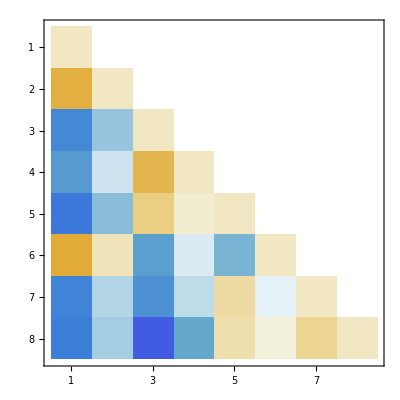
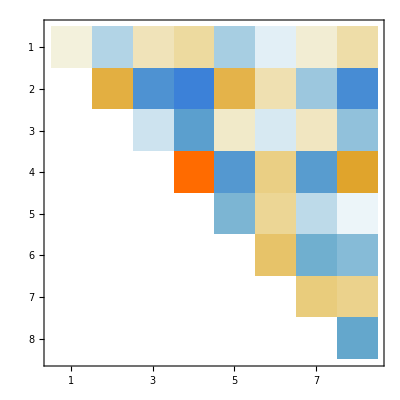

```mathematica
m=8;
A=RandomReal[{-1,1},{m,m}];
(* Start Script *)
L=IdentityMatrix[m];
U=A; 
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}]
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

### Function

```mathematica
LU[A_]:=Module[{m=Length[A],L,U=A},
(* Start Script *)
L=IdentityMatrix[m];
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
{L,U}
]
```

1.63021×10^-14

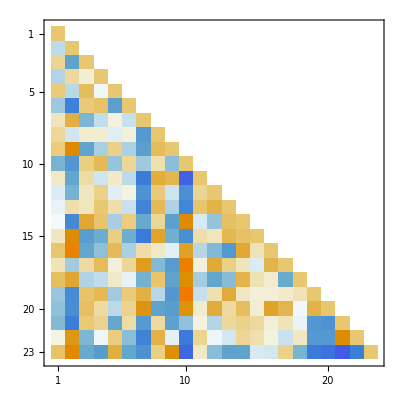
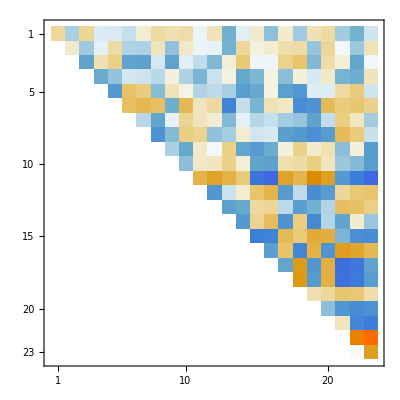

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}];
{L,U}=LU[A];
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

## Solving a Linear System with an LU Decomposition

We know how to solve triangular systems. we even know that the obvious algorithm is backwards stable. We now know how to split a matrix up into two triangular matrices A=L.U.  we should be able to put this together to get an algorithm to solve A.x=L.U.x=b. All we need to do is make up an intermediate variable.  y=U.x 
	L.(U.x)=L.y=b
Solve L.y=b to get a ỹ.  Then solve U.x=ỹ to get x̃.  Since the triangular solves are backwards stable this would all be great if the L.U decomposition was stable!  It is not!

### Need for Pivoting

There are perfectly well behaved linear systems which will break our first attempt at an LU decomposition.  For example
	(ϵ | 1.0
1.0 | 1.0).(x1
x2)=(b1
b2).
In exact arithmetic Gaussian elimination gives the solution
	x1 | = | (b1-b2)/(-1+ϵ) | ⟶ | b2-b1
x2 | = | (-b1+b2 ϵ)/(-1+ϵ) | ⟶ | b1
The system is fine as ϵ→0.  Our first attempt at an LU decomposition gives. 
	A=(ϵ | 1.0
1.0 | 1.0)=(1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | 1-ϵ^-1)
which in exact arithmetic works just fine: exact arithmetic does not care that ϵ^-1 could be huge. On any computer this is a real problem!  When ϵ is small in floating point the last entry gets messed up and we will get 
	 (1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | -ϵ^-1)=(ϵ | 1
1 | 0)

The sad thing is this has nothing to do with the equations/matrix. As ϵ→0 the condition number κ(A) is the singular value ratio of ratio of (0 | 1.0
1.0 | 1.0) which is roughly 3.

The really sad thing is that if we had just written down the equations in a different order we would have got (1.0 | 1.0
ϵ | 1.0)=(1 | 0
ϵ | 1)(1 | 1
0 | 1-ϵ) which would have worked just fine.

We can not write a usage guide for a function that says “make sure your equations” are in a decent order. We need to make an algorithm that reorders the equations (rows in the matrix) into a good order on the fly.

The first question is given a matrix A which row (same as equation) should we start with.

After the first row we just ask which of the remaining rows is best to do next.

The resulting algorithm is called an LU decomposition with row pivoting.

You can also ask which remaining variable (column of the matrix would be best) which gives column pivoting.

If you ask which is the best variable and equation you are doing complete pivoting!